# Clase G - Mediciones

## Dump

Pruebas:

- Polarizacion
- Ganancia de tension
- Sensibilidad
- Potencia de salida
- Ancho de banda: a 100mV. Barro hasta ver arriba y abajo cuando cae en 3dB, con grador y oscilo
- Slew rate: le meto una cuadrada de 500mV
- Impedancia de entrada: frecs 100, 1k, 10k. Nah, sin carga, 500mV
- Impedancia de salida: Ver con oscilo como baja con carga conocida. foto
- Distorsion: a 100, 1k, 10k, a 1w y 100w. Lo tengo que traducir a dB relativo 
- Intermodulacion: ver el efecto, no se bien como se mide. Meterle frecs de 1k y 1k3Hz	
- Rechazo de riple

```mathematica
20/8.
```

2.5

```mathematica
0.3 8
```

2.4

```mathematica
18.7/0.22
```

85.

```mathematica
20/Sqrt[2]/8.
```

1.76777

## Pasos para hoy

## General

```mathematica
SetDirectory["C:\\CUBASE\\Test proj\\Audio"];
```

```mathematica
SetDirectory@NotebookDirectory[];
```

```mathematica
Needs["SyntaxExtensions`"];
```

```mathematica
potAInputPico[pot_]:=Sqrt[2]/40 potAOutputPico[pot]
potAOutputRMS[pot_]:=Sqrt[pot 8]
potAOutputPico[pot_]:=potAOutputRMS[pot]*Sqrt[2]
vpico[db_]:=1.5 10^(db/20)
vdb[pico_]:=-3.52183+8.68589 Log[pico]
vdb2[pico_?QuantityQ]:=vdb2[pico~QuantityMagnitude~IndependentUnit["dB"]]
vdb2[pico_]:=20 Log10[pico]-6.88
```

-22 va a 1W

```mathematica
Sqrt[8] Sqrt[2]//N
```

4.

```mathematica
Solve[10^((-16+offset)/10)==10, offset, Reals]//N
```

{{offset→26.}}

```mathematica
20 Log10[23.]
```

27.2346

```mathematica
vdbToPow[db_?QuantityQ]:=Quantity[10^((QuantityMagnitude[db, IndependentUnit["dB"]]+26.)/10), "Watts"]
vdbToPow[db_]:=10^((db+26.)/10)
vdbToPowPos[db_]:=vdbToPow[-db]~SetPrecision~2;
```

```mathematica
vdbToPow[Quantity[-16, IndependentUnit["dB"]]]
```

10. W

```mathematica
powToPico[w_]:=Sqrt[w 8] Sqrt[2.]
```

```mathematica
vdbToPow[-16.]
```

39.8107

```mathematica
powToPico[10]
```

12.6491

```mathematica
10 10/8/2.
```

6.25

```mathematica
40
```

```mathematica
powToDb[40.]
```

16.0206

```mathematica
dbAmp[l_List]:=20 Log10[l]//alignMax;
dbAmp[l_]:=20 Log10[l];
```

```mathematica
alignMax[l_]:=l-Max[l];
```

```mathematica
audioTake[aud_, l_] := Audio@Sound`SoundTake[Sound`AudioToSound[aud], l]
```

```mathematica
dbToPow[l_]:=10^(l/10);
powToDb[l_]:=10 Log10[l]
totalDbPow=dbToPow/*Total/*powToDb;
dbToPercentage[d_]:=UnitConvert[dbToPow[d], "Percent"]
```

## Polarizacion

El multiplicador de Vbe se coloca en la tension que genera una corriente de 200mA, medida a traves de la caida por la resistencia de emisor

```mathematica
0.0095/0.22
```

0.0431818

La salida sin entrada es de 4mV

## Ganancia

A entrada de 200mV pico pico de entrada. Salida, 4.96V pico pico, 195Hz

```mathematica
ganancia195=4.96/0.2;
```

A entrada de 206mV pico pico de entrada. Salida, 4.96V pico pico, 195Hz

```mathematica
ganancia1k=4.96/0.206;
```

```mathematica
ganancia1k
```

24.0777

```mathematica
40/Sqrt[2.]
```

28.2843

## Resistencia de entrada

Todas a 100mV pico

### A 100Hz

14kOhms.

### A 1kHz

14kOhms.

### A 10kHz

10kOhms.

## Resistencia de salida

Todas a 100mV pico

```mathematica
Solve[8/(8+rout)4.48==4.44]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{rout→0.0720721}}

```mathematica
Solve[8/(8+rout)4.48==4.36]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{rout→0.220183}}

### A 100Hz

Salida 4.48V pico pico sin carga
Con carga de 8, 4.68V

### A 1kHz

Salida 4.48V pico pico sin carga
Con carga de 8, 4.44V

### A 10kHz

Salida 4.48V pico pico sin carga
Con carga de 8, 4.36

## Ancho de banda

El ancho de banda medido a 3dB va de 6.6Hz hasta 225kHz. 
La senial de salida era de 2.12V a la salida, o entrada de 85mV

## Slew Rate

## THD

```mathematica
CopyFile["Audio 01_41.wav",FileNameJoin[{NotebookDirectory[],"thd-2mW.wav"}]];
```

```mathematica
in=Import["in.wav"];
```

```mathematica
rin=removeAudioSilences[in];
```

```mathematica
Duration[in]
```

36.4694 s

```mathematica
getIntervals[removeAudioSilences@in,0.05]
```

{{0.05,1.90125}}

```mathematica
AudioIntervals[rin,#ModifiedKullbackLeibler<0.5&& #SpectralCrest>800 &&#SpectralKurtosis>500&&#SpectralFlatness<0.00001&,1]
```

{{7.06167,8.96646},{9.05938,10.9642}}

```mathematica
AudioIntervals[rin,#SpectralCrest>1000&,1]
```

{{0.0464583,2.97333},{3.06625,6.96875},{7.06167,8.96646},{9.05938,10.9642},{11.0571,12.9619},{15.0525,16.9573},{26.0631,27.9679}}

```mathematica
AudioIntervals[rin,#SpectralFlatness<0.00001&,1]
```

{{7.06167,8.96646},{9.05938,10.9642}}

```mathematica
AudioIntervals[rin,#SpectralSpread<20&,1]
```

{{7.06167,8.96646}}

```mathematica
AudioIntervals[rin,#SpectralKurtosis>1500&,1]
```

{}

### Versión usando built-ins

```mathematica
getIntervals[aud_, pad_]:=AudioIntervals[aud,#ModifiedKullbackLeibler<0.05&,1]/.{b_Real,e_Real}:>{b+pad, e-pad}
octaveStep[freqs_List]:=Nearest[octaveStepCandidates,Mean@Differences[Log2@freqs], 1]//First;
baseFreq[freqs_List, step_]:=MapIndexed[{fr,ind}↦With[{in=First[ind]-1},fr 2^-(in step)],freqs]//Mean//Round[#, 5]&
octaveStepCandidates={1, 1/3};
cleanupFreqs[freqs_]:=With[{st=octaveStep[freqs]},baseFreq[freqs, st] 2^(st Range[0, Length@freqs-1])]
window[l_, w_]:=winOfLen[w, Length@l]l
winOfLen[w_, n_Integer?Positive]:=w@Subdivide[-0.5, 0.5, n+1][[2;;-2]]
```

Ahora a calcular la distorsión

```mathematica
Clear[getHarmonic, getSpec, getHarmonics];
getSpec[saud_Audio]:=TimeSeries[20 Log10@Abs@Fourier[window[AudioData[saud], BlackmanWindow], FourierParameters->{1, -1}]//alignMax,{0., saud~AudioMeasurements~"SampleRate"}];
getHarmonic[ts_,baseFreq_, n_, pad_:0.2]:=With[{freqCenter=baseFreq (n+1)},
	Max@TimeSeriesWindow[ts,  freqCenter+pad baseFreq {-1, 1}]/;
		freqCenter<Quotient[ts["LastTime"],2]];
getHarmonic[ts_, baseFreq_, n_, pad_:0.2]:=Nothing;
getHarmonics[ts_, baseFreq_, nmax_, pad_:0.2]:=getHarmonic[ts, baseFreq, #, pad]&/@Range@nmax;
```

```mathematica
Clear[processThd];
processThd[freq_, aud_, num_:10]/;freq>AudioMeasurements[aud,"SampleRate"]/4:=Nothing
processThd[freq_, aud_, num_:10]:=Quantity[freq,"Hertz"]->Let[
	{ts, getSpec[aud]},
	{harms, getHarmonics[ts, freq, num]},
	{nwaves, 3},
	{audmore, AudioResample[aud, Round[100 freq]]~audioTake~QuantityMagnitude[Duration@aud/2+Quantity[nwaves/2{-1, 1}/freq, "Seconds"],"Seconds"]},
	{nsr, AudioMeasurements[audmore, "SampleRate"]},
	{exwave, TimeSeries[AudioData[audmore], {0, Automatic,1/nsr}]},
	<|"THD"->dbToPercentage@totalDbPow@harms, "Harmonics"->dbToPercentage/@harms, "Example wave"->getTsFirstWave@exwave|>
	]
```

```mathematica
removeAudioSilences[aud_, thr_:0.01]:=AudioDelete[aud,AudioIntervals[aud,#RMSAmplitude<thr&]]
```

```mathematica
Clear[getThd];
getThd[aud_Audio, silenceThresh_:0.02]:=Let[
	{noSilAud, removeAudioSilences[aud, silenceThresh]},
	{sr, noSilAud~AudioMeasurements~"SampleRate"},
	{auds, audioTake[noSilAud,#]&/@getIntervals[noSilAud, 0.02]},
	{freqs, AudioMeasurements[auds,"SpectralCentroid"]//cleanupFreqs},
	{aufrec,AssociationThread[freqs, auds]},
	
	Dataset@Association@KeyValueMap[processThd, aufrec]
	]
getThd[fname_String,st_:0.02]:=With[{aud=Import[fname]}, getThd[aud,st]/;AudioQ@aud];
```

```mathematica
getTsFirstWave[ts_]:=TimeSeriesWindow[ts,Transpose@Normal@Sign[ts]/.{times_, vals_}:> (SequencePosition[vals, {-1, 1}][[;;2]]//Flatten//times[[#[[{1, -1}]]]]&)]
```

### General

#### Barrido en frecuencia

Necesito código que tome un Audio, que arranca y termina con silencio o ruidito (y quizá con algún valor de ayuda semiautomático), lo seccione en las partes según frecuencia, y devuelva la association de <| frec -> <| thd -> , by harmonic -> {} |>|>

La frecuencia la puedo meter a mano somehow. Not sure.

Las principales tareas son las de recortar principio y final y seccionar por frecuencia

##### Recortar principio y final

Puedo tomar un moving average de la potencia

```mathematica
sr=rin~AudioMeasurements~"SampleRate"
```

48000

```mathematica
wlen=2^13;woffset=2^10;
sp=Abs@SpectrogramArray[rin, wlen,woffset, BlackmanWindow][[All,;;wlen~Quotient~2]]//Map[GaussianFilter[#,3]&];
```

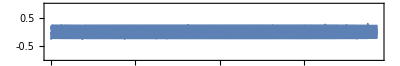

```mathematica
AudioPlot[10 rin]
```

```mathematica
Quantile[Abs[Import["in.wav"]//removeAudioSilences],0.95]
```

0.0243834

```mathematica
FileNames["*.wav"]
```

{in.wav,out-divisor.wav,out-no-divisor.wav,sweep-sin-extra-carga-divisor1k-14dB.wav,thd-10w.wav,thd-1W.wav,thd-2mW.wav}

```mathematica
Quantile[Abs[Import["out-no-divisor.wav"]//removeAudioSilences],0.95]
```

0.525969

```mathematica
0.5259687900543213/0.02438342571258545
```

21.5708

```mathematica
localMax=(Sign@Differences[#]~SequencePosition~{1, -1}//Map[Mean]//N//ReplaceAll[i_?NumericQ/;i<20/48000 wlen->Nothing])&/@sp;
```

```mathematica
Clear[cleanAndCheck];
cleanAndCheck[w_List]:=With[{res=w~MedianFilter~10~GaussianFilter~5},res/;AllTrue[Differences@res,NonNegative]]
_cleanAndCheck:=Throw["Bad check"]
```

```mathematica
localMaxWeights=Function[{pow, maxs},First@MaximalBy[maxs,Interpolation[pow]]]@@@Transpose@{sp, localMax};
cleanLocalMaxWeights=cleanAndCheck[localMaxWeights];
```

```mathematica
Clear[buildSections];
buildSections[{},{}]:={};
buildSections[{}, {e_}]:={{1, e}};
buildSections[{b_}, {}]:={{b, -1}};
buildSections[{b_,rb___}, {e_,re___}]/;e<b:=buildSections[{1,b,  rb}, {e, re}];
buildSections[{bb___, lb_}, {be___,le_}]/;le<lb &&Positive[le]:=buildSections[{bb, lb}, {be, le, -1}];
buildSections[bl_List, be_List]/;Length@bl==Length@be:=With[{res=Transpose@{bl, be}},res/;OrderedQ[Flatten@res//DeleteCases[-1]]]
_buildSections:=Null/;(Throw["Bad buildSections"];False)
```

```mathematica
sects=Let[
{indx,Boole@Map[#<1&,Differences@cleanLocalMaxWeights]},
{ends,SequencePosition[indx,{1,0}][[All,1]]},
{begs,SequencePosition[indx,{0,1}][[All,2]]},
buildSections[begs, ends]
];
```

```mathematica
sects
```

{{1,464},{468,510},{516,557},{563,602},{610,649},{657,696},{704,742},{752,789},{799,836},{846,882},{894,929},{941,975},{987,1022},{1034,1069},{1081,1116},{1128,1163},{1175,1210},{1222,1257},{1269,1304},{1316,1350},{1362,1397},{1409,-1}}

```mathematica
sampleToFreq[sr_,wlen_][sfreq_]:=sr/wlen sfreq
```

```mathematica
freqs=Take[cleanLocalMaxWeights,#]&/@sects//Map[Mean]//sampleToFreq[sr, wlen];
```

```mathematica
freqs
```

{72.1261,201.785,254.727,319.009,401.242,506.616,635.454,799.711,1004.77,1262.54,1584.96,2000.98,2516.6,3166.99,3981.45,5012.7,6313.48,7948.24,10004.9,12594.7,15852.5,19954.1}

```mathematica
cleanupFreqs[freqs]//N
```

{155.,195.288,246.047,310.,390.576,492.094,620.,781.151,984.189,1240.,1562.3,1968.38,2480.,3124.6,3936.75,4960.,6249.21,7873.51,9920.,12498.4,15747.,19840.}

```mathematica
Differences@Log10@freqs//Mean
```

0.299972

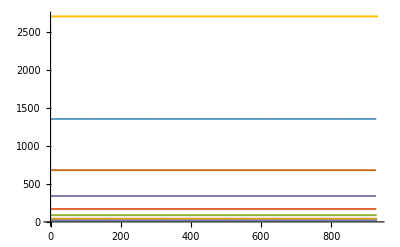

```mathematica
ListPlot[Take[cleanLocalMaxWeights,#]&/@sects]
```

#### Barrido en amplitud

### Many

Necesito pasar de dB a valor.

Tengo la misma cosa medida con y sin divisor. Y puedo más o menos medirla con multímetro en AC.

```mathematica
FileNames["*.wav"]
```

{in.wav,out-divisor.wav,out-no-divisor.wav,sweep-sin-extra-carga-divisor1k-14dB.wav,thd-10w.wav,thd-16dB.wav,thd-18dB.wav,thd-1W.wav,thd-20dB.wav,thd-22dB.wav,thd-24dB-v2.wav,thd-24dB.wav,thd-26dB.wav,thd-28dB.wav,thd-2mW.wav,thd-30dB.wav,thd-32dB.wav,thd-34dB.wav,thd-36dB.wav}

```mathematica
div=Import["out-divisor.wav"];
noDiv=Import["out-no-divisor.wav"];
```

```mathematica
divFactor=Quantile[Abs[noDiv], 0.95]/Quantile[Abs[div], 0.95];
```

```mathematica
divFactor=34;
```

```mathematica
thds[KeyMap[vdb2]][Keys]
```

Dataset[<>]

```mathematica
pico/.Solve[vdb[pico]==-16]//First
```

0.237734

```mathematica
?vpico
```

Global`vpico

vpico[db_]:=1.5 10^(db/20)

```mathematica
vpico[-16]
```

0.237734

-15.9986

```mathematica
0.35 29
```

10.15

```mathematica
Quantile[Abs@Import["thd-24dB.wav"], 0.98] divFactor
```

1.20853

```mathematica
0.09464366347771491 /divFactor
```

```mathematica
auds=AssociationMap[Import,FileNames["thd-*dB*.wav"]];
```

```mathematica
thds=getThd[#,0.003]&/@auds;
```

```mathematica
thds=Dataset[thds/.d_Dataset:>Normal@d]//Normal/*Dataset;
```

```mathematica
thds=thds[All, <|"Freqs"->#|>&];
```

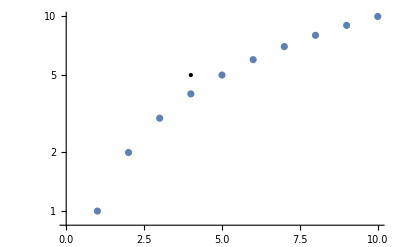

```mathematica
ListLogPlot[Range@10, Epilog->{PointSize[Large],Point[{{4, Log@5}}]}]
```

```mathematica
plotThd[tst_]:=ListLogLogPlot[tst, Epilog->{PointSize[Medium],Point[Transpose@{Keys@tst~QuantityMagnitude~"Hertz"//Log, Values@tst~QuantityMagnitude~"Percent"//Log}]}, Joined->True, PlotTheme->"Detailed", FrameLabel->{"f (Hz)", "THD (%)"}]
```

```mathematica
thds=thds[All,Prepend[#, "Plot"->Query["Freqs",plotThd, "THD"]@#]&];
```

```mathematica
thds=thds[All,KeyMap[N[#,3]&]];
```

```mathematica
thds=thds[All,Prepend[#, "Plot"->Query[ListLinePlot, "THD"]@#]&];
```

```mathematica
thds=thds//Normal//Dataset;
```

```mathematica
thds=thds[KeyDrop["thd-24dB-v2.wav"]];
```

```mathematica
thds=thds[KeyMap[StringReplace["thd-"~~(x__)~~"dB.wav":>x]/*ToExpression/*(Quantity[#, IndependentUnit["dB"]]&)]];
```

```mathematica
thds[All,{"Freqs"->Query[All,{"Example wave"->(ListLinePlot[#, Axes->False]&), "Harmonics"->(Column@Take[SetPrecision[#, 2], UpTo[4]]&)}]}]
```

Dataset[<>]

```mathematica
thds[TabView,"Plot"]
```

1234567891011

```mathematica
Export["some.mx",thds];
```

```mathematica
SetDirectory@NotebookDirectory[];
```

```mathematica
thds=Import["some.mx","MX"];
```

### A 2mW

```mathematica
res2mw=getThd["thd-2mW.wav"];
```

```mathematica
res2mw[All, {"THD"->(SetPrecision[#, 2]&),"Example wave"->(ListLinePlot[#, Axes->False]&), "Harmonics"->(Column@Take[SetPrecision[#, 2], UpTo[4]]&)}]
```

Dataset[<>]

### A 1W

#### Generate

```mathematica
pot=1;
vrms=Sqrt[pot 8.];
vvpico=vrms Sqrt[2];
vin=vvpico/40 Sqrt[2]//N;
```

```mathematica
vin
```

0.141421

```mathematica
potAInputPico[vin]
```

0.053183

```mathematica
vdb[vin]
```

-20.5115

#### Analyse

```mathematica
SetDirectory@NotebookDirectory[];
```

```mathematica
res1w=getThd["thd-1W.wav"];
```

```mathematica
res1w[All, {"THD"->(SetPrecision[#, 2]&),"Example wave"->(ListLinePlot[#, Axes->False]&), "Harmonics"->(Column@Take[SetPrecision[#, 2], UpTo[4]]&)}]
```

Dataset[<>]

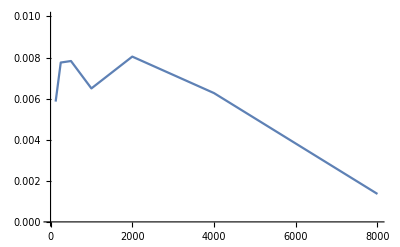

```mathematica
ListLinePlot[Normal@res1w[All, "THD"], PlotRange->{0, 0.01}]
```

### A 14dB

```mathematica
ast=getThd["sweep-sin-extra-carga-divisor1k-14dB.wav"];
```

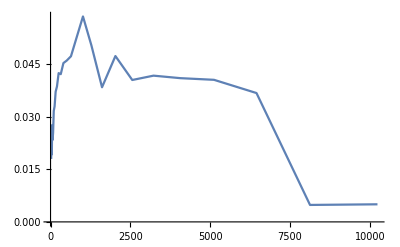

```mathematica
ast[ListLinePlot, "THD"]
```

```mathematica
ast[All, {"THD"->(SetPrecision[#, 2]&),"Example wave"->(ListLinePlot[#, Axes->False]&), "Harmonics"->(Column@Take[SetPrecision[#, 2], UpTo[4]]&)}][KeyMap[N[#,3]&]]
```

Dataset[<>]

### A 10W

#### Generate

```mathematica
pot=10;
vrms=Sqrt[pot 8.];
vvpico=vrms Sqrt[2];
vin=vvpico/40 Sqrt[2]//N;
```

```mathematica
vin
```

0.447214

```mathematica
vvpico
```

12.6491

```mathematica
potAInputPico[vin]
```

0.0945742

```mathematica
vdb[vin]
```

-10.5115

#### Analyse

```mathematica
SetDirectory@NotebookDirectory[];
```

```mathematica
res10w=getThd["thd-10w.wav"];
```

```mathematica
res10w[All, {"THD"->(SetPrecision[#, 2]&),"Example wave"->(ListLinePlot[#, Axes->False]&), "Harmonics"->(Column@Take[SetPrecision[#, 2], UpTo[4]]&)}]
```

Dataset[<>]

### A 100W

#### Generate

```mathematica
vrms=1/8.;
vvpico=vrms Sqrt[2];
vin=vvpico/40 Sqrt[2]//N;
```

```mathematica
vin
```

0.00625

```mathematica
potAInputPico[vin]
```

0.0111803

```mathematica
vdb[vin]
```

-47.6042

#### Analyse

```mathematica
res100w=getThd["thd-100w.wav"];
```

$Aborted

```mathematica
res100w
```

## Intermodulacion

```mathematica
aud=Import["C:\\CUBASE\\Test proj\\Audio\\Audio 01_19.wav"];
```

Import::nffil: File not found during Import.

```mathematica
dat=AudioData[aud][[1]];
```

AudioData::audio: Expecting an audio object instead of $Failed.

```mathematica
f=TimeSeries[Abs@Fourier[dat], {0, 48000}];
```

Fourier::fftl: Argument $Failed is not a non-empty list or rectangular array of numeric quantities.

```mathematica
ListLinePlot[20 Log10@TimeSeriesWindow[f, {0, 400}]//alignMax, PlotRange->Full]
```

ListLinePlot::lpn: 0. is not a list of numbers or pairs of numbers.

ListLinePlot[0,PlotRange→Full]

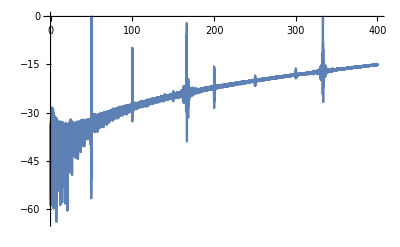

O sea, 0dB aca es aprox 1.5V pico de salida. Cada 20dB es dividir por 10 supongo.

```mathematica
1.5 10^(db/20)==vpico//Solve
```

{{db→-3.52183+8.68589 Log[vpico]}}

```mathematica
potAOutputPico[100.]
```

40.

```mathematica
potAInputPico[1]//vdb
```

-20.5115

```mathematica
potAInputPico[1]//N
```

0.141421

```mathematica
8/0.3
```

26.6667

```mathematica
70./1000
```

0.07

```mathematica
0.07^2 30
```

0.147

## Eficiencia

Si se despreciando el consumo de energía en polarización y sólo se tiene en cuenta la lo disipado por la rama de alta corriente entre las fuentes y la carga, en señal, se obtiene una cota para la eficiencia del amplificador en función de la tensión de salida y la de las fuentes. Sea P_L la potencia consumida por la carga y P_T la de los transistores, se tiene

```mathematica
Clear[plMean, ptMean]
pl[rl_,vo_][t_]:=vo[t]^2/rl
pt[vf_,rl_, vo_][t_]:=(vf[Abs[vo[t]]]-Abs[vo[t]]) Abs[vo[t]/rl]
plMean[vo:{__Real}, rl_]:=vo.vo/rl/Length[vo]
plMean[{vo_, per_}, rl_]:=Integrate[pl[rl, vo][t], {t, 0, per}]/per
ptMean[vo:{__Real}, vf_, rl_]:=Sum[(vf[Abs[vvo]]-Abs[vvo]) Abs[vvo/rl], {vvo, vo}]/Length[vo]
ptMean[{vo_, per_},vf_, rl_]:=NIntegrate[pt[vf, rl, vo][t], {t, 0, per}]/per
Clear[ef];
ef[vo:{__Real}, vf_, rl_]:=With[{pl=plMean[vo, rl],
	pt=ptMean[vo, vf, rl]}, 
	pl/(pl+pt)];
ef[{vo_, per_}, vf_,rl_]:=With[{pl=plMean[{vo, per}, rl],
pt=ptMean[{vo, per}, vf, rl]}, 
pl/(pl+pt)]//Simplify
ef[{a_?NumericQ, vo_, per_}, vf_, rl_]:=ef[{a vo@#&, per}, vf, rl]
```

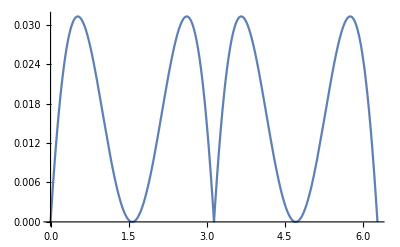

```mathematica
Plot[pt[1&, 8, Sin][t], {t,0, 2 π}]
```

P_L(t)=(v_o(t))^2/R_L
P_T(t)=(V_FA(v_o)-|v_o(t)|)(|v_o(t)|)/R_L

Para un clase B que recibe su máxima excursión recibiendo una onda senoidal, y asumiendo que esta es igual a la tensión de la fuente, devuelve una cota de eficiencia de π/4=78%.

Este valor depende tanto de la amplitud de la onda como de la forma de onda. Mientras más tiempo se pase con la salida a tensión similar a la fuente, menos potencia se desperdicia. En la figura XX se aprecian las rectas de eficiencia óptima en función de la excursión de la onda para senoidales, cuadradas y triangulares

```mathematica
ef[{a Sin[#]&, 2 π}, 1&, 8]
```

(a^2 π)/(a^2 π+4 Abs[a]-π Abs[a]^2)

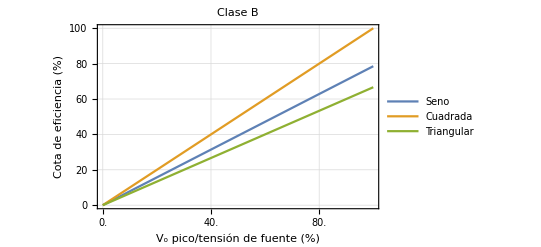

```mathematica
Plot[{100ef[{a, Sin[#]&, 2 π}, 1&, 8],100ef[{a, SquareWave[#]&, 1}, 1&, 8],100 ef[{a, TriangleWave[#]&, 1}, 1&, 8]},{a, 0, 1}, Evaluated->True, PlotLegends->{"Seno", "Cuadrada", "Triangular"}, PlotTheme->"Detailed", FrameLabel->{"V_o pico/tensión de fuente (%)", "Cota de eficiencia (%)"}, FrameTicks->{{Automatic,None},{{#, 100#}&@Range[0, 1, 0.2]//Thread,None}}, PlotLabel->"Clase B"]
```

```mathematica
Export["ef1.pdf",-Graphics-];
```

Si el audio es de baja potencia pero contiene picos que requieren alta potencia el clase B es muy ineficiente. Un clase G mejora esto

```mathematica
Clear[vfg]
vfg[vl_, vh_][vo_]:=Piecewise[{{vl, Abs[vo]<vl}, {vh, True}}]
(*vfg[vl_, vh_][vo_]/;vo<vl:=vl
vfg[vl_, vh_][vo_]/;vo≥vl:=vh*)
```

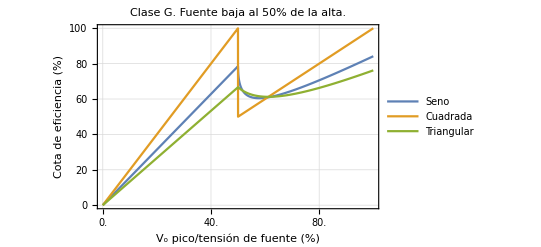

```mathematica
Plot[{100 ef[{a ,Sin[#]&, 2 π},vfg[0.5, 1] , 8],100 ef[{a, SquareWave[#]&, 1}, vfg[0.5, 1], 8],100 ef[{a, TriangleWave[#]&, 1}, vfg[0.5, 1], 8]},{a, 0, 1}, Evaluated->True, PlotLegends->{"Seno", "Cuadrada", "Triangular"}, PlotTheme->"Detailed", FrameLabel->{"V_o pico/tensión de fuente (%)", "Cota de eficiencia (%)"}, FrameTicks->{{Automatic,None},{{#, 100#}&@Range[0, 1, 0.2]//Thread,None}}, PlotLabel->"Clase G. Fuente baja al 50% de la alta."]
```

```mathematica
Export["ef2.pdf", -Graphics-];
```

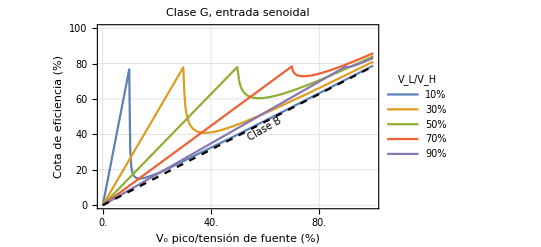

```mathematica
Plot[Table[100ef[{a, Sin[#]&, 2 π},vfg[r, 1] , 8], {r, 0.1, 0.9, 0.2}]//Evaluate,{a, 0, 1}, Evaluated->True, PlotLegends->LineLegend[Table[QuantityForm[Round@UnitConvert[r, "Percent"], "Abbreviation"], {r, 0.1, 0.9,0.2}], LegendLabel->"V_L/V_H"], PlotTheme->"Detailed", FrameLabel->{"V_o pico/tensión de fuente (%)", "Cota de eficiencia (%)"}, FrameTicks->{{Automatic,None},{{#, 100#}&@Range[0, 1, 0.2]//Thread,None}}, PlotLabel->"Clase G, entrada senoidal", PlotPoints->5, MaxRecursion->6]~Show~Plot[100ef[{a, Sin[#]&, 2 π}, 1&, 8], {a, 0, 1}, PlotStyle->{Black, Dashed}]~Show~Graphics[{Text[Style["Clase B", FontSize->10]~Rotate~(30 Degree), {0.6, 43}]}]~Show~(PlotRange->{0, 100})
```

```mathematica
Export["ef3.pdf", -Graphics-];
```

Para mejor aprovechamiento de las fuentes de forma eficiente, la fuente baja debe colocarse en un valor que la active la mayor parte del tiempo mientras que la alta debe capturar los posibles spikes en volumen. El valor óptimo depende del uso típico. Cada género de películas, de audio, etc, puede dar valores diferentes. Para una entrada senoidal de máxima excursión, la efeiciencia máxima es de 86% cuando la tensión baja V_L es un 70.7% de la alta.

```mathematica
Block[{NIntegrate=Integrate},ef[{Sin, 2 π}, vfg[r, 1], 8]]~FullSimplify~(0<r<1)
```

(π √(1-r^2))/(4+4 r (-1+(-1+r) r+√(1-r^2)))

```mathematica
Maximize[{%, 0≤r≤1}, r]
```

{π/(4 √2 (1-1/(2 √2))),{r→1/(√2)}}

```mathematica
N[%]
```

{0.859097,{r→0.707107}}

```mathematica
got=Import["/home/rui/Downloads/got.wav"];
```

```mathematica
gotDat=AudioData[got]//Mean;
```

```mathematica
Mean@gotDat//Dimensions
```

{167669760}

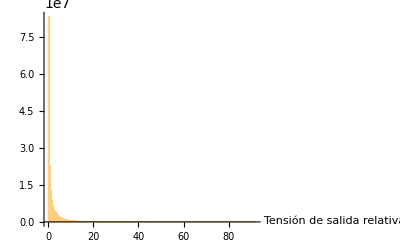

```mathematica
Histogram[Rescale[100Abs@gotDat, {0, 1}],Axes->{True, False}, PlotRange->Full , AxesLabel->{"Tensión de salida relativa (%)", None}]
```

```mathematica
Export["hist-got.pdf", -Graphics-];
```

```mathematica
l=BlockMap[Max, Abs@gotDat,1*^6, 2*^5];
```

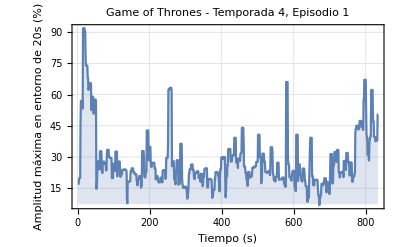

```mathematica
ListLinePlot[100l, PlotRange->Full, Filling->Axis,   PlotTheme->"Detailed", FrameLabel->{"Tiempo (s)", "Amplitud máxima en entorno de 20s (%)"}, PlotRangePadding->0, PlotLabel->"Game of Thrones - Temporada 4, Episodio 1"]
```

```mathematica
Export["vol-got.pdf", -Graphics-];
```

```mathematica
e:efgot[ds_, r_]:=e=ef[gotDat~Downsample~ds, vfg[r, 1], 8]
```

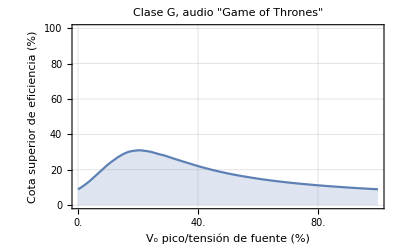

```mathematica
Plot[100efgot[1000, r],{r, 0, 1}, PlotPoints->6, MaxRecursion->4,PlotTheme->"Detailed", FrameLabel->{"V_o pico/tensión de fuente (%)", "Cota superior de eficiencia (%)"}, FrameTicks->{{Automatic,None},{{#, 100#}&@Range[0, 1, 0.2]//Thread,None}},PlotLegends->None, PlotLabel->"Clase G, audio \"Game of Thrones\" ", Filling->Axis, PlotRange->{0, 100}]
```

```mathematica
Export["ef-got.pdf", -Graphics-];
```

Se puede ver que la máxima eficiencia se logra con V_L≃V_H/5

```mathematica
pf=Import["/home/rui/pf.wav"];
```

```mathematica
pfDat=AudioData[pf]//Mean;
```

```mathematica
pfDat//Dimensions
```

{19869535}

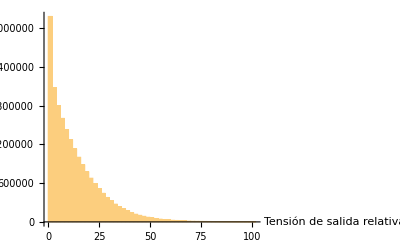

```mathematica
Histogram[Rescale[100Abs@pfDat, {0, 1}],Axes->{True, False}, PlotRange->Full , AxesLabel->{"Tensión de salida relativa", None}]
```

```mathematica
Export["hist-pf.pdf", -Graphics-];
```

```mathematica
l=BlockMap[Max, Abs@pfDat,50000, 1*^4];
```

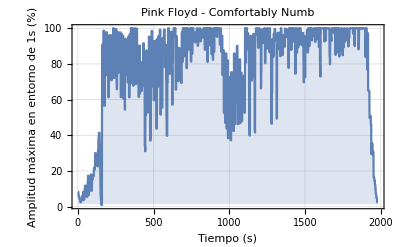

```mathematica
ListLinePlot[100l, PlotRange->Full, Filling->Axis,   PlotTheme->"Detailed", FrameLabel->{"Tiempo (s)", "Amplitud máxima en entorno de 1s (%)"}, PlotRangePadding->0, PlotLabel->"Pink Floyd - Comfortably Numb" ]
```

```mathematica
Export["vol-pf.pdf", -Graphics-];
```

```mathematica
e:efPf[ds_, r_]:=e=ef[pfDat~Downsample~ds, vfg[r, 1], 8]
```

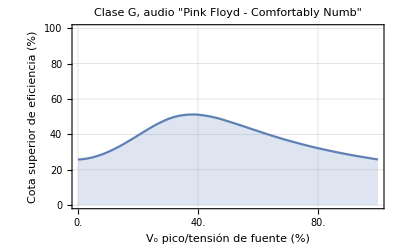

```mathematica
Plot[100efPf[100, r],{r, 0, 1}, PlotTheme->"Detailed", FrameLabel->{"V_o pico/tensión de fuente (%)", "Cota superior de eficiencia (%)"}, FrameTicks->{{Automatic,None},{{#, 100#}&@Range[0, 1, 0.2]//Thread,None}},PlotLegends->None, PlotLabel->"Clase G, audio \"Pink Floyd - Comfortably Numb\" ", Filling->Axis, PlotRange->{0, 100}]
```

```mathematica
Export["ef-pf.pdf", -Graphics-];
```

Se puede observar que, por sus volumenes más parejos, este audio ofrece una eficiencia máxima cuando V_L≃0.37 V_H, mayor que en el caso anterior.

Ahora bien, hay otros factores que alejan al amplificador armado de la cota antes mencionada.

Consumo de las primeras dos etapas

Potencia de polarización de los transistores de potencia internos. Esto depende de la corriente fijada por el multiplicador de Vbe (reduce la distorsión de crossover haciendo funcionar al amplificador en modo AB) y de la tensión de la fuente V_L.

Márgenes de tensión para mantener a los transistores polarizados y evitar que entren en saturación. En el caso de los transistores de potencia internos, esto se debe a los V_BE requeridos para que se encuentren activados tanto él como su driver, y también con con cuánto exceso de tensión de bias se coloca en serie con el multiplicador de Vbe para asegurar que los transistores de potencia externos se activan antes de que saturen los internos.  En el caso de los externos, esto ocurre cuando la máxima excursión del amplificador no está determinada por la posible saturación de los transistores de potencia externos sino por límites de otros componentes, o por la saturación del transistor del VAS. En este último caso, esto puede reducirse utilizando una fuente separada, de baja potencia, para alimentar a las primeras dos etapas con una tensión levemente superior.

Colocando al multiplicador de Vbe de forma tal que circulen aproximadamente 200mA en polarización por los transistores internos de potencia, consume 400mA V_L en stand-by. Es decir, para V_L=15V, consume 6W, que representa el 6% del máximo consumo. Ahora bien, en señal, a medida que la carga requiere corriente, se va desactivando un transistore de potencia y entonces la eficiencia no se ve reducida significativamente salvo cargas bajas o audios con muchos momentos de silencio o señales de muy baja amplitud.

En nuestro amplificador, se separó la alimentación de la tercera etapa de las dos primeras partes, principalmente, para poder entregar una tensión mayor a las primeras dos etapas evitando la pérdida de eficiencia mencionada anteriormente. Habría sido más óptimo también alimentar al driver de la etapa de potencia Q2 y Q8 con esa fuente de tensión superior. En este amplificador, que polariza con 30mA circulando por el VAS y con resistencias de emisor de 100Ω, los transistores del VAS Q14 y Q9 ya comienzan a saturar cuando los V_CE de los transistores de potencia externos están a 5V de saturar. Estos 5V producen un derroche de eficiencia importante.

Se coloca una resistencia de valor bajo como 0.1Ω en serie con cada una de las fuentes de potencia y se mide con osciloscopio la caída de tensión en ella para una entrada senoidal de máxima excursión y frecuencia 1kHz. Simultáneamente se mide la salida. De esta forma se estima la corriente que entrega la fuente y su potencia en función de la tensión de entrada. Con esto se puede calcular la eficiencia aproximada para dicha entrada, y estimar la eficiencia frente a cualquier entrada como las mencionadas anteriormente.

Conoclusiones. Faltarían protecciones. El PCB fue diseñado para incorporar protección contra sobrecorriente por cortocircuito o carga demasiado alta. Sin embargo, faltarían protecciones a componentes sensibles. Por ejemplo, si  la es mayor a la especificada y satura, hay spikes de alta potencia en los drivers del VAS Q13 y Q10, que no pueden tolerar.

## Eficiencia

```mathematica
vo[t_]:=Sin[2 π 1000 t]20
```

```mathematica
ihl1[t_]:=Piecewise[{{0.7+1.9Sin[2 π t], Abs@Mod[t-0.25,1, -0.5]<0.34/2}, {0, True}}]
ihl2[t_]:=Piecewise[{{-0.7+1.9Sin[2 π t], 0.75-0.34/2<Mod[t,1]<0.75+0.34/2}, {0, True}}]
```

```mathematica
ill1[t_]:=Piecewise[{{0, 0.75-0.4/2<Mod[t,1]<0.75+0.4/2}, {0, 0.25-0.34/2<Mod[t, 1]<0.25+0.34/2}, {0.7+1.9Sin[2 π t], True}}]
ill2[t_]:=Piecewise[{{0, 0.25-0.4/2<Mod[t,1]<0.25+0.4/2}, {0, 0.75-0.34/2<Mod[t, 1]<0.75+0.34/2}, {-0.7+1.9Sin[2 π t], True}}]
```

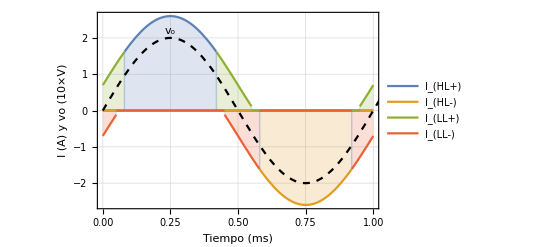

```mathematica
Plot[{ihl1[t], ihl2[t],ill1[t], ill2[t]}, {t, 0, 1}, PlotRange->Full, Filling->Axis, PlotTheme->"Detailed", PlotRangeClipping->False, PlotLegends->{"I_(HL+)", "I_(HL-)", "I_(LL+)", "I_(LL-)"}, FrameLabel->{"Tiempo (ms)", "I (A) y vo (10×V)"}]~Show~Plot[Sin[2 π t]2, {t, 0, 1}, PlotStyle->Directive[Dashed,Black]]~Show~Graphics[{Text["v_o", {0.25, 2.2}]}]
```

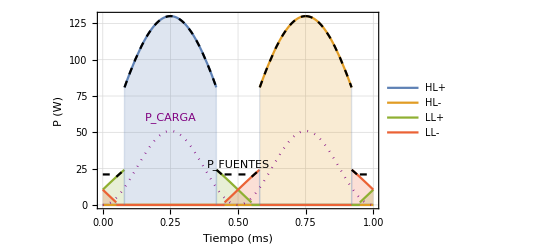

```mathematica
Plot[{Abs[ihl1[t] 50], Abs[ihl2[t] 50],Abs[ill1[t] 15], Abs[ill2[t] 15]}, {t, 0, 1}, PlotRange->Full, Filling->Axis, PlotTheme->"Detailed", PlotRangeClipping->False, PlotLegends->{"HL+", "HL-", "LL+", "LL-"}, FrameLabel->{"Tiempo (ms)", "P (W)"}]~Show~Plot[{Abs[ihl1[t] 50], Abs[ihl2[t] 50],Abs[ill1[t] 15], Abs[ill2[t] 15]}//Total, {t, 0, 1}, PlotStyle->Directive[Dashed,Black]]~Show~Graphics[{Text["P_FUENTES", {0.5, 28}]}]~Show~Plot[(20Sin[2 π t])^2/7.85, {t, 0, 1}, PlotStyle->Directive[Thick, Dotted, Purple]]~Show~Graphics[{Text[Style["P_CARGA",Purple], {0.25, 60}]}]
```

```mathematica
Export["ef-pots.pdf", -Graphics-];
```

```mathematica
ptot[t_]:=5 (3 √((Piecewise[{{0, 0.04999999999999999<Mod[t,1]<0.45||0.58<Mod[t,1]<0.92}, {-0.7+1.9 Sin[2 π t], True}}])^2)+3 √((Piecewise[{{0, 0.55<Mod[t,1]<0.95||0.07999999999999999<Mod[t,1]<0.42000000000000004}, {0.7+1.9 Sin[2 π t], True}}])^2)+10 (√((Piecewise[{{-0.7+1.9 Sin[2 π t], 0.58<Mod[t,1]<0.92}, {0, True}}])^2)+√((Piecewise[{{0.7+1.9 Sin[2 π t], Abs[Mod[-0.25+t,1,-0.5]]<0.17}, {0, True}}])^2)));
```

```mathematica
pload[t_]:=(20Sin[2 π t])^2/7.85
```

```mathematica
efMed[plo_]:=plo/ptot[InverseFunction[pload][plo]]
```

```mathematica
ploadvo[vo_]:=vo^2/7.85
ptotvo[vo_]:=ptot[ArcSin[vo/20]/(2 π)]
```

```mathematica
ArcSin[0.1/20]/(2 π)
```

0.000795778

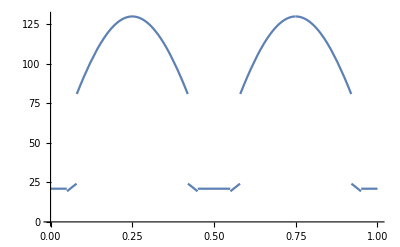

```mathematica
Plot[ptot[t], {t, 0, 1}]
```

InverseFunction::ifun: Inverse functions are being used. Values may be lost for multivalued inverses.

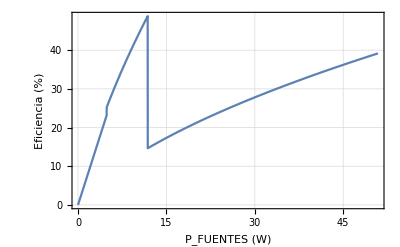

```mathematica
Plot[100 efMed[plo], {plo, 0, 50.9}, PlotTheme->"Detailed",Exclusions->None, FrameLabel->{"\!\(\*SubscriptBox[\(P\), \(FUENTES\)]\) (W) ","Eficiencia (%)"}, PlotLegends->None]
```

```mathematica
Export["ef-rel.pdf", -Graphics-];
```

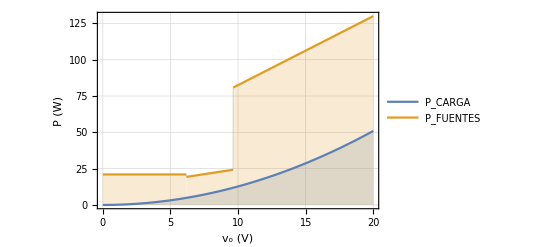

```mathematica
Plot[{ploadvo[vo], ptotvo[vo]}, {vo, 0, 20}, PlotTheme->"Detailed", PlotRange->Full, Filling->Axis, PlotTheme->"Detailed", PlotRangeClipping->False, PlotLegends->{"P_CARGA", "P_FUENTES"}, FrameLabel->{"v_o (V)", "P (W)"}]
```

```mathematica
Export["ef-rel.pdf", -Graphics-];
```

```mathematica
Directory[]
```

/mnt/froot/home/rui/gclass/mediciones

```mathematica
Export["ef-rec.pdf", -Graphics-];
```

```mathematica
ploadvo[20 pfDat]
```

```mathematica
ptotvo[20 pfDat];
```

```mathematica
20 pfDat
```